```mathematica
FFru[Q_]:=(0.1069*Exp[-49.4238*((Q/(4.0*Pi))^2)] + 
1.1912*Exp[-12.7417*((Q/(4.0*Pi))^2)] + 
-0.3176*Exp[-4.9125*((Q/(4.0*Pi))^2)] + 
0.0213)^2
k=0;
Dynamic[k]
PowderAvgScatt[Q_,d0_,Psi_,d_]:=(1.0/9.0)*FFru[Q]*NIntegrate[(Sin[theta])*(1/(4  Pi))*(1+2 Cos[Q d0 Sin[theta]Cos[Psi+Phi]])^2 *(1-Cos[Q d  Sin[theta]Cos[Phi-Psi]]),{theta,0,Pi},{Phi,0,2*Pi},Method-> "QuasiMonteCarlo",MaxPoints-> 7000]
PowderAvgScattElastic[Q_,d0_,Psi_,d_]:=(1.0/9.0)*NIntegrate[(Sin[theta])*(1/(4  Pi))*(1+2 Cos[Q d0 Sin[theta]Cos[Psi+Phi]])^2 *(Cos[Q d  Sin[theta]Cos[Phi-Psi]]),{theta,0,Pi},{Phi,0,2Pi},Method-> "QuasiMonteCarlo",MaxPoints-> 7000]
PowderAvgAnalytic[Q_,d0_,Psi_,d_]:=(FFru[Q]/9)*(3+2Sin[2Q d0]/(2 Q d0)+4Sin[Qd0]/(Qd0)-(3Sin[Qd]/(Qd)+2Sin[QSqrt[4d0^2+d^2]]/(QSqrt[4d0^2+d^2])+4Sin[QSqrt[d0^2+d^2]]/(QSqrt[d0^2+d^2])))
PowderAvgScattFFonly[Q_,d0_]:=(1.0/9.0)*FFru[Q]*NIntegrate[(Sin[theta])*(1/(4  Pi))*(1+2 Cos[Q d0 Cos[Phi]])^2 ,{theta,0,Pi},{Phi,0,2*Pi},Method-> "QuasiMonteCarlo",MaxPoints-> 7000]
```

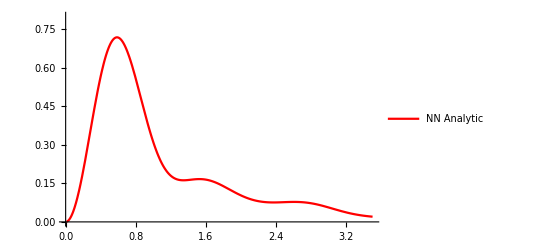

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.00504504 and 0.0000778421 for the integral and error estimates.

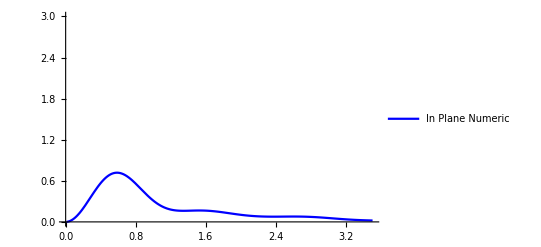

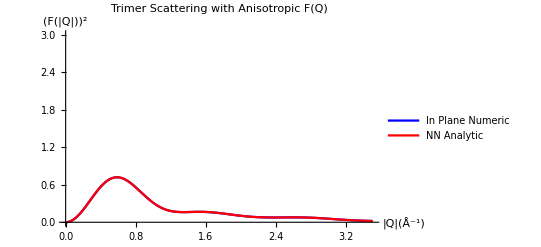

```mathematica
pinplanean= Plot[PowderAvgAnalytic[Q,2.54,Pi/4,5.76],{Q,0.01,3.5},PlotRange-> {{0,3.5},{0,0.8}},PlotLegends->{"NN Analytic"},PlotStyle->Red]
pinplane = Plot[PowderAvgScatt[Q,2.54,Pi/4,5.76],{Q,0.01,3.5},PlotRange-> {{0,3.5},{0,3}},PlotLegends->{"In Plane Numeric"},PlotStyle->Blue]

ptot=Show[pinplane,pinplanean,PlotLabel-> "Trimer Scattering with Anisotropic F(Q)",AxesLabel-> {"|Q|(Å^-1)","(F(|Q|))^2"}]
```

```mathematica
]
```

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.020114 and 0.000310293 for the integral and error estimates.

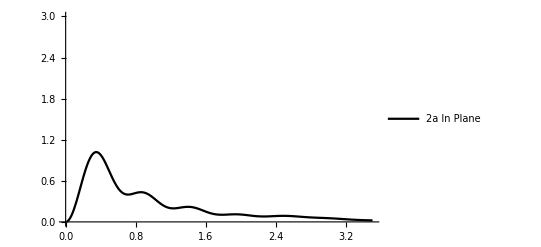

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0154717 and 0.000238754 for the integral and error estimates.

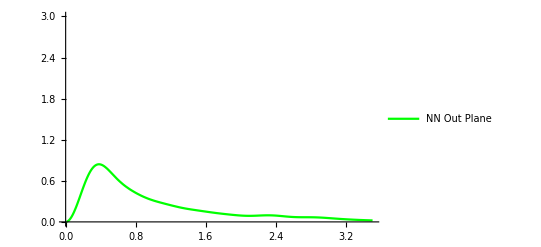

NIntegrate::inumr: The integrand ((1+2 Cos[0.0255551 Cos[Plus[«2»]] Sin[theta]])^2 Sin[theta])/(4 π) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand 0.0795775 (1.+2. Cos[0.0255551 Cos[Plus[«2»]] Sin[theta]])^2 Sin[theta] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
p2ainplane = Plot[PowderAvgScatt[Q,2.54,Pi/4,11.504],{Q,0.01,3.5},PlotRange-> {{0,3.5},{0,3}},PlotLegends->{"2a In Plane"},PlotStyle->Black]
pnnout = Plot[PowderAvgScatt[Q,2.54,0.5*73.4*Pi/180 + Pi/4,10.09],{Q,0.01,3.5},PlotRange-> {{0,3.5},{0,3}},PlotLegends->{"NN Out Plane"},PlotStyle->Green]
pFF = Plot[PowderAvgScattFFonly[Q,2.54],{Q,0.01,3},PlotRange->{{0,3.5},{0,3}},PlotLegends->{"FF"},PlotStyle->Grey]
```

```mathematica
Export["inplane_nn.dat",Table[PowderAvgScatt[Q,2.54,Pi/4,5.76],{Q,0.01,3.5,0.02}]]
Export["inplane_nnn.dat",Table[PowderAvgScatt[Q,2.54,0.000,9.97],{Q,0.01,3.5,0.02}]]
Export["inplane_2a.dat",Table[PowderAvgScatt[Q,2.54,0.000,11.504],{Q,0.01,3.5,0.02}]]
Export["nn_outplane.dat",Table[PowderAvgScatt[Q,2.54,73.4*Pi/180,10.09],{Q,0.01,3.5,0.02}]]
```

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.00497388 and 0.0000767442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0446748 and 0.000689195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.123597 and 0.00190611 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

inplane_nn.dat

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0149041 and 0.000229986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.133329 and 0.00205306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.365912 and 0.00561068 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

inplane_nnn.dat

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.01984 and 0.000306134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.177251 and 0.00272797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.485172 and 0.00742858 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

inplane_2a.dat

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0152535 and 0.000235352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.136498 and 0.00210222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.374849 and 0.00575184 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

nn_outplane.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["inplane_nnn.dat"]]]
```

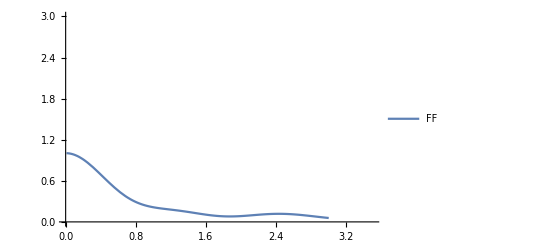

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 4.53182 and 0.0455231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 4.35262 and 0.0457956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 4.18022 and 0.0460558 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

q_avg_ff.dat

```mathematica
pFF = Plot[PowderAvgScattFFonly[Q,2.54],{Q,0.01,3},PlotRange->{{0,3.5},{0,3}},PlotLegends->{"FF"},PlotStyle->Grey]
Export["q_avg_ff.dat",Table[PowderAvgScattFFonly[Q,2.54],{Q,0.01,3.5,0.02}]]
```

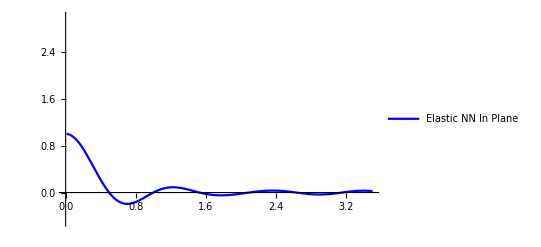

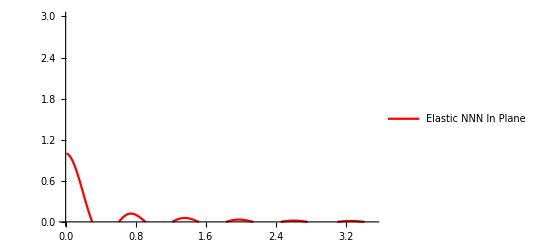

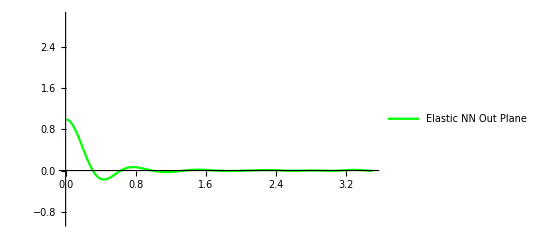

```mathematica
pinplane = Plot[PowderAvgScattElastic[Q,2.54,Pi/4,5.76],{Q,0.01,3.5},PlotRange-> {{0,3.5},{-0.5,3}},PlotLegends->{"Elastic NN In Plane"},PlotStyle->Blue]
pnnninplane = Plot[PowderAvgScattElastic[Q,2.54,Pi/4,9.97],{Q,0.01,3.5},PlotRange-> {{0,3.5},{0,3}},PlotLegends->{"Elastic NNN In Plane"},PlotStyle->Red]
pnnout = Plot[PowderAvgScattElastic[Q,2.54,Pi/4 + 73.4*Pi/180,10.09],{Q,0.01,3.5},PlotRange-> {{0,3.5},{-1,3}},PlotLegends->{"Elastic NN Out Plane"},PlotStyle->Green]
```

```mathematica
Export["inplane_nn_el.dat",Table[PowderAvgScattElastic[Q,2.54,0.0000,5.76],{Q,0.01,3.5,0.02}]]
Export["inplane_nnn_el.dat",Table[PowderAvgScattElastic[Q,2.54,0.000,9.97],{Q,0.01,3.5,0.02}]]
Export["nn_outplane_el.dat",Table[PowderAvgScattElastic[Q,2.54,73.4*Pi/180,10.09],{Q,0.01,3.5,0.02}]]
Export["trimerff_avg.dat",Table[PowderAvgScattFFonly[Q,2.54],{Q,0.01,3.5,0.02}]]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 2.89978 and 0.0335737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 2.6742 and 0.0354498 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 2.50477 and 0.0369434 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

inplane_nn_el.dat

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 3.09823 and 0.0320488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 2.67316 and 0.035316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 2.28748 and 0.038653 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

inplane_nnn_el.dat

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 1.72304 and 0.0258399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.953792 and 0.0286016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.389462 and 0.0311488 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

nn_outplane_el.dat

trimerff_avg.dat